```mathematica
SetDirectory@NotebookDirectory[]
Import["../esmlib_nsl.wl"]
```

/home/eric/git/nonlinear-systems-lab/Project 1

## Import data

```mathematica
{times,xs}=Transpose@Import["data/cleaned/rocking1.tsv"][[2;;All,1;;2]];
times = times-Min[times];
```

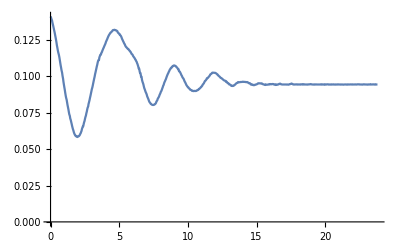

```mathematica
ListLinePlot[Transpose@{times,xs}]
```

## Build a model

```mathematica
ClearAll[x]
```

```mathematica
diffeq=x''[t]==-k x[t]-b x'[t];
initial={x[0]==x0,x'[0]==v0};
```

```mathematica
Manipulate[Module[{sol},
sol=NDSolve[{diffeq, initial}/.<|k->p`k,b->p`b,x0->p`x0,v0->p`v0|>,x[t],{t,0,Max@times}][[1]];
IFPlot[sol]],{p`k,0,1},{p`b,0,1},{p`x0,0,1},{p`v0,0,1}]
```

## Fit the model

```mathematica
x[t]/.sol
```

1/(2 √(b^2-4 k))(-2 ⅇ^(1/2 (-b-√(b^2-4 k)) t) v0+2 ⅇ^(1/2 (-b+√(b^2-4 k)) t) v0-b ⅇ^(1/2 (-b-√(b^2-4 k)) t) x0+b ⅇ^(1/2 (-b+√(b^2-4 k)) t) x0+ⅇ^(1/2 (-b-√(b^2-4 k)) t) √(b^2-4 k) x0+ⅇ^(1/2 (-b+√(b^2-4 k)) t) √(b^2-4 k) x0)

```mathematica
sol=DSolve[{diffeq,initial},x[t],t][[1]]
```

{x[t]→1/(2 √(b^2-4 k))(-2 ⅇ^(1/2 (-b-√(b^2-4 k)) t) v0+2 ⅇ^(1/2 (-b+√(b^2-4 k)) t) v0-b ⅇ^(1/2 (-b-√(b^2-4 k)) t) x0+b ⅇ^(1/2 (-b+√(b^2-4 k)) t) x0+ⅇ^(1/2 (-b-√(b^2-4 k)) t) √(b^2-4 k) x0+ⅇ^(1/2 (-b+√(b^2-4 k)) t) √(b^2-4 k) x0)}

```mathematica
fit=FindFit[Transpose[{times, xs-.0935}][[10;;All]],x[t]/.sol,{{k,2},{b,.3},{x0,.1},v0},t]
```

FindFit::nrlnum: The function value {0.00571358-1.23805×10^-18 ⅈ,0.00551783+2.4761×10^-18 ⅈ,0.00524459+2.4761×10^-18 ⅈ,0.00496304-2.4761×10^-18 ⅈ,0.00485715+0. ⅈ,«41»,-0.00676317+0. ⅈ,-0.00712817+0. ⅈ,-0.00698695+0. ⅈ,-0.0071766+0. ⅈ,«658»} is not a list of real numbers with dimensions {708} at {k,b,x0,v0} = {1.98465,0.292267,0.0549077,-0.0282542}.

{k→1.98465,b→0.292267,x0→0.0549077,v0→-0.0282542}

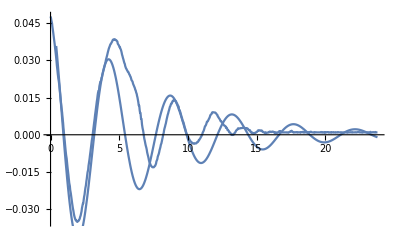

```mathematica
Show[ListLinePlot[Transpose@{times,xs-.0935}],Plot[x[t]/.(sol/.fit),{t,0,Max[times]}]]
```

```mathematica
sol/.fit
```

{x[t]→(0.-0.178422 ⅈ) ((0.0404607+0.153871 ⅈ) ⅇ^((-0.146134-1.40118 ⅈ) t)-(0.0404607-0.153871 ⅈ) ⅇ^((-0.146134+1.40118 ⅈ) t))}

```mathematica
FindFit[Transpose@{times, xs},1/(2 √(b^2-4 k))(-2 ⅇ^(1/2 (-b-√(b^2-4 k)) t) v0+2 ⅇ^(1/2 (-b+√(b^2-4 k)) t) v0-b ⅇ^(1/2 (-b-√(b^2-4 k)) t) x0+b ⅇ^(1/2 (-b+√(b^2-4 k)) t) x0+ⅇ^(1/2 (-b-√(b^2-4 k)) t) √(b^2-4 k) x0+ⅇ^(1/2 (-b+√(b^2-4 k)) t) √(b^2-4 k) x0),{k,b,x0,v0},t]
```

FindFit::nrjnum: The Jacobian is not a matrix of real numbers at {k,b,x0,v0} = {1.,1.,1.,1.}.

{k→1.,b→1.,x0→1.,v0→1.}

```mathematica
Manipulate[Module[{sol},
sol=NDSolve[{diffeq, initial}/.<|k->p`k,b->p`b,x0->p`x0,v0->p`v0|>,x[t],{t,0,Max@times}][[1]];
Show[ListLinePlot[Transpose@{times,xs-offset}],IFPlot[sol]]],{p`k,0,2},{p`b,0,1},{p`x0,0,.1},{p`v0,-.1,.1},{{offset,.0935},0,.2}]
```